## Parallel Solow and Langevin

Solow growth:
dk/dt=s(k)f(k)-(δ+n)k
where we have the production function f(k)=Ax^α_1 and the savings rate s (k) = s_1+(s_2-s_1)/(1+ⅇ^(-s_3(k-d))) 
Solow growth can be written as
dx/dt=s(x)f(x)-(δ+n)x
dx/dt=s(x)f(x)-λx

Langevin dynamics:
dx/dt=-β dF/dx+σ dW/dt
where left term is deterministic, while right term is stochastic
F: energy landscape

### Simplified Solow model + Potential

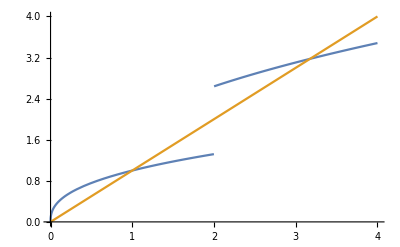

FindArgMin::fmgz: Encountered a gradient that is effectively zero. The result returned may not be a minimum; it may be a maximum or a saddle point.

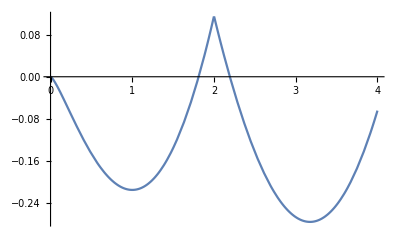

NIntegrate::nlim: y = x is not a valid limit of integration.

General::stop: Further output of NIntegrate::nlim will be suppressed during this calculation.

0.463062

NIntegrate::nlim: y = x is not a valid limit of integration.

General::stop: Further output of NIntegrate::nlim will be suppressed during this calculation.

0.463062

```mathematica
ClearAll[U,τ,δP];

A=10;α1=0.4;s1=0.1;s2=0.2;s3=10;d=2;n=0.5;

(* Solow growth *)
f[x_]:=A x^α1;
s[x_]:=If[x≤d,s1,s2]
δP[x_]:=If[x<1.95&&x>1.85,0.5,0.5];
Depreciation[x_]:=(δP[x]+n) x

Plot[{f[x] s[x],Depreciation[x]},{x,0,4}]

(* Potential based on Langevin dynamics *)
U[x_]=-(Integrate[f[x] s[x]-Depreciation[x],x]);
xmin1=#&@@FindArgMin[U[x],{x,1}];
xmin2=#&@@FindArgMin[U[x],{x,3}];
U2[x_?NumericQ]:=U[x/L];
Plot[Evaluate[U[x]],{x,0,4}]

(* MFPT *)
L=1;
sol=FindRoot[τ==L NIntegrate[Exp[-U2[x]] NIntegrate[Exp[U[y]],{y,x/L,1}],{x,0,1}] ,{τ,1}];
τ=τ/.sol
sol=FindRoot[τ==L NIntegrate[Exp[-U2[x]] NIntegrate[Exp[U[y]],{y,x/L,1}],{x,0,L}] ,{τ,1}];
τ=τ/.sol
```

#### Original Solow model + Potential

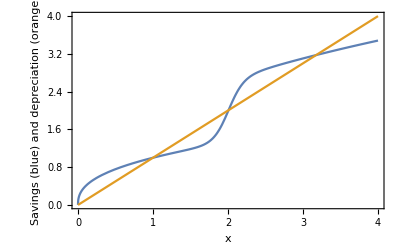

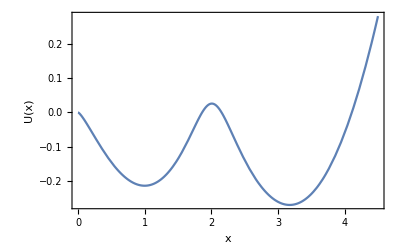

NIntegrate::nlim: y = x is not a valid limit of integration.

General::stop: Further output of NIntegrate::nlim will be suppressed during this calculation.

{τ→0.463062}

NIntegrate::nlim: y = x is not a valid limit of integration.

General::stop: Further output of NIntegrate::nlim will be suppressed during this calculation.

{τ→0.463062}

NIntegrate::nlim: y = x is not a valid limit of integration.

General::stop: Further output of NIntegrate::nlim will be suppressed during this calculation.

{τ→0.463062}

NIntegrate::nlim: y = 0.5 x is not a valid limit of integration.

General::stop: Further output of NIntegrate::nlim will be suppressed during this calculation.

{τ→1.36361}

NIntegrate::nlim: y = 0.5 x is not a valid limit of integration.

General::stop: Further output of NIntegrate::nlim will be suppressed during this calculation.

{τ→1.85225}

NIntegrate::nlim: y = 0.5 x is not a valid limit of integration.

General::stop: Further output of NIntegrate::nlim will be suppressed during this calculation.

{τ→0.780315}

NIntegrate::nlim: y = 0.333333 x is not a valid limit of integration.

General::stop: Further output of NIntegrate::nlim will be suppressed during this calculation.

{τ→2.24439}

NIntegrate::nlim: y = 0.333333 x is not a valid limit of integration.

General::stop: Further output of NIntegrate::nlim will be suppressed during this calculation.

```mathematica
ClearAll[f,s,Depreciation,U,int,int2,sol,τ];

A=10;α1=0.4;s1=0.1;s2=0.2;s3=10;d=2;δP=0.5;n=0.5;

(* Solow growth *)

f[x_]:=A x^α1;
s[x_]:=s1+(s2-s1)/(1+Exp[-s3 (x-d)]); 
Depreciation[x_]:=(δP+n) x

(* Potential based on Langevin dynamics *)
Plot[{f[x] s[x],Depreciation[x]},{x,0,4},Frame->True, FrameLabel->{"x", "Savings (blue) and
 depreciation (orange)"}]

int=NDSolveValue[{U'[x]==-(f[x]s[x] -Depreciation[x]),U[0]==0},U,{x,0,4.5}];
Plot[int[x],{x,0,4.5},Frame->True,FrameLabel->{"x","U(x)"},Axes->False]

(* MFPT *)
L=1;
int2[x_?NumericQ]:=int[x/L];
sol=FindRoot[τ==L NIntegrate[Exp[-int2[x]] NIntegrate[Exp[int[y]],{y,x/L,1}],{x,0,1}] ,{τ,1}]
sol=FindRoot[τ==L NIntegrate[Exp[-int2[x]] NIntegrate[Exp[int[y]],{y,x/L,1}],{x,0,L}] ,{τ,1}]
sol=FindRoot[τ==L NIntegrate[Exp[-int2[x]] NIntegrate[Exp[int[y]],{y,x/L,1}],{x,0,1/L}] ,{τ,1}]

L=2;
int2[x_?NumericQ]:=int[x/L];
sol=FindRoot[τ==L NIntegrate[Exp[-int2[x]] NIntegrate[Exp[int[y]],{y,x/L,1}],{x,0,1}] ,{τ,1}]
sol=FindRoot[τ==L NIntegrate[Exp[-int2[x]] NIntegrate[Exp[int[y]],{y,x/L,1}],{x,0,L}] ,{τ,1}]
sol=FindRoot[τ==L NIntegrate[Exp[-int2[x]] NIntegrate[Exp[int[y]],{y,x/L,1}],{x,0,1/L}] ,{τ,1}]

L=3;
int2[x_?NumericQ]:=int[x/L];
sol=FindRoot[τ==L NIntegrate[Exp[-int2[x]] NIntegrate[Exp[int[y]],{y,x/L,1}],{x,0,1}] ,{τ,1}]
sol=FindRoot[τ==L NIntegrate[Exp[-int2[x]] NIntegrate[Exp[int[y]],{y,x/L,1}],{x,0,L}] ,{τ,1}]
sol=FindRoot[τ==L NIntegrate[Exp[-int2[x]] NIntegrate[Exp[int[y]],{y,x/L,1}],{x,0,1/L}] ,{τ,1}]

L=4;
int2[x_?NumericQ]:=int[x/L];
sol=FindRoot[τ==L NIntegrate[Exp[-int2[x]] NIntegrate[Exp[int[y]],{y,x/L,1}],{x,0,1}] ,{τ,1}]
sol=FindRoot[τ==L NIntegrate[Exp[-int2[x]] NIntegrate[Exp[int[y]],{y,x/L,1}],{x,0,L}] ,{τ,1}]
sol=FindRoot[τ==L NIntegrate[Exp[-int2[x]] NIntegrate[Exp[int[y]],{y,x/L,1}],{x,0,1/L}] ,{τ,1}]
```

## Changing parameters in Solow

#### Parameter A

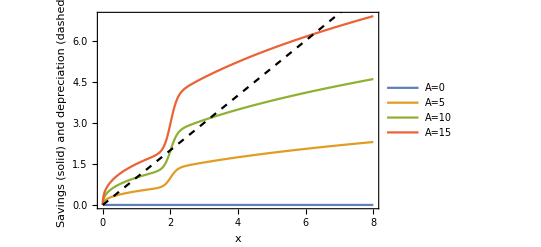

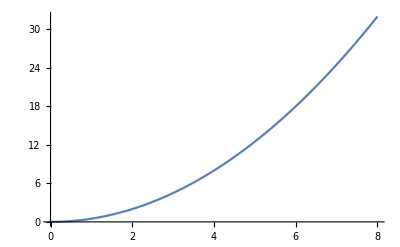
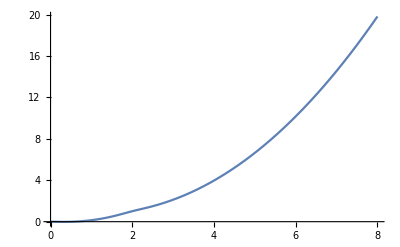
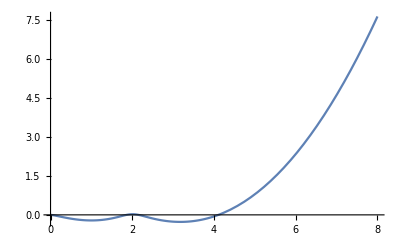
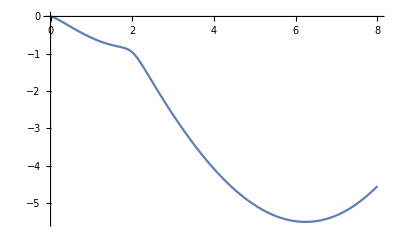

```mathematica
α1=0.4;s1=0.1;s2=0.2;s3=10;d=2;δP=0.5;n=0.5;

f[x_]:=A x^α1;
s[x_]:=s1+(s2-s1)/(1+Exp[-s3 (x-d)]); 
Depreciation[x_]:=(δP+n) x
Savings[x_]:=s[x] f[x]

ValuesA={0,5, 10,15};
p1=Plot[Evaluate[Table[Savings[x], {A, ValuesA}]], {x,0,8},
Frame->True, FrameLabel->{"x", "Savings (solid) and
 depreciation (dashed)"},
LabelStyle->Medium,PlotLegends->Placed[Table[Row[{"A=",x}],{x,ValuesA}],{Left,Top}]];
p2=Plot[Depreciation[x],{x,0,8},PlotStyle->{Black,Dashed}];
Show[{p1,p2}]

Evaluate[Table[int=NDSolveValue[{U'[x]==-(f[x]s[x] -Depreciation[x]),U[0]==0},U,{x,0,8}];
Plot[int[x],{x,0,8}],{A, ValuesA}]]
(* int:=NDSolveValue[{U'[x]==-(Savings[x] -Depreciation[x]),U[0]==0},U,{x,0,8}]
Plot[Evaluate@Table[int[x],{A,ValuesA}],{x,0,8},PlotRange->{-4,10}] *)
```

#### Parameter α1

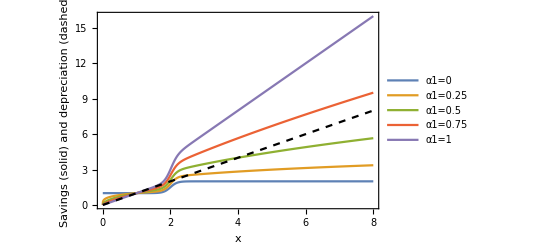

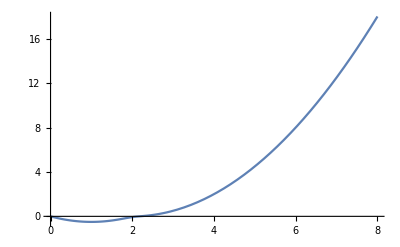
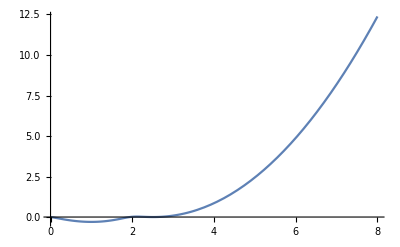
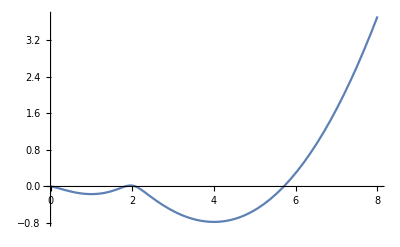
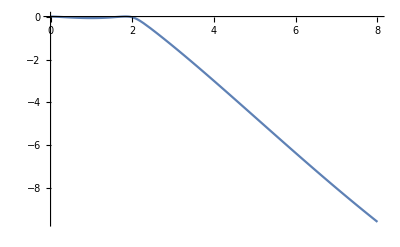
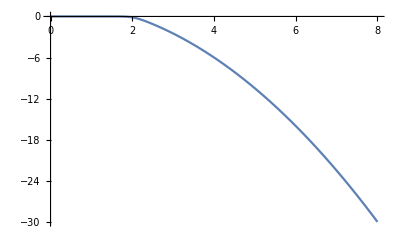

```mathematica
A=10;s1=0.1;s2=0.2;s3=10;d=2;δP=0.5;n=0.5;

f[x_]:=A x^α1;
s[x_]:=s1+(s2-s1)/(1+Exp[-s3 (x-d)]); 
Depreciation[x_]:=(δP+n) x
Savings[x_]:=s[x] f[x]

Valuesα1={0, 0.25,0.5,0.75,1};
p1=Plot[Evaluate[Table[Savings[x], {α1, Valuesα1}]], {x,0,8},
Frame->True, FrameLabel->{"x", "Savings (solid) and
 depreciation (dashed)"},
LabelStyle->Medium,PlotLegends->Placed[Table[Row[{"α1=",x}],{x,Valuesα1}],{Left,Top}]];
p2=Plot[Depreciation[x],{x,0,8},PlotStyle->{Black,Dashed}];
Show[{p1,p2}]

Evaluate[Table[int=NDSolveValue[{U'[x]==-(f[x]s[x] -Depreciation[x]),U[0]==0},U,{x,0,8}];
Plot[int[x],{x,0,8}],{α1, Valuesα1}]]
(* int:=NDSolveValue[{U'[x]==-(Savings[x] -Depreciation[x]),U[0]==0},U,{x,0,8}]
Plot[Evaluate@Table[int[x],{α1, Valuesα1}],{x,0,8},PlotRange->{-4,10}] *)
```

#### Parameter s1

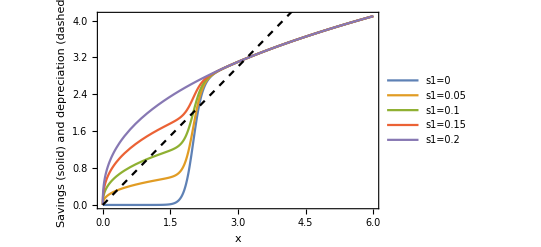

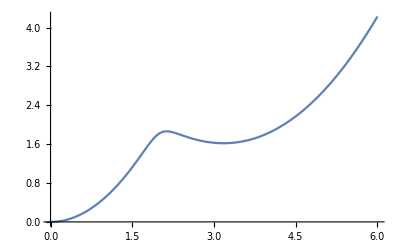
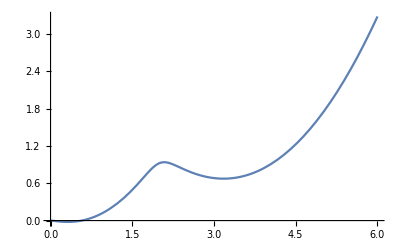
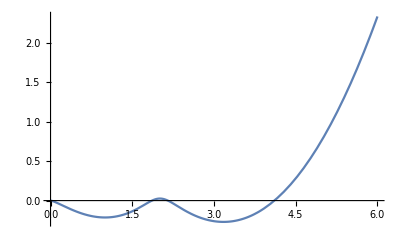
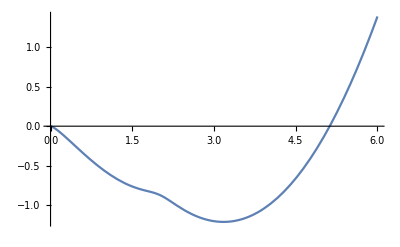
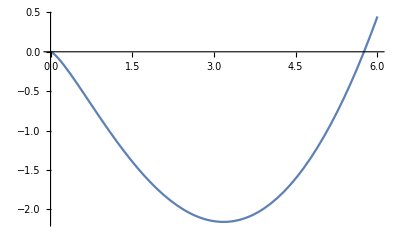

```mathematica
A=10;α1=0.4;s2=0.2;s3=10;d=2;δP=0.5;n=0.5;

f[x_]:=A x^α1;
s[x_]:=s1+(s2-s1)/(1+Exp[-s3 (x-d)]); 
Depreciation[x_]:=(δP+n) x
Savings[x_]:=s[x] f[x]

Valuess1={0,0.05,0.1,0.15,0.2};
p1=Plot[Evaluate[Table[Savings[x], {s1, Valuess1}]], {x,0,6},
Frame->True, FrameLabel->{"x", "Savings (solid) and
 depreciation (dashed)"},
LabelStyle->Medium,PlotLegends->Placed[Table[Row[{"s1=",x}],{x,Valuess1}],{Right,Bottom}]];
p2=Plot[Depreciation[x],{x,0,6},PlotStyle->{Black,Dashed}];
Show[{p1,p2}]

Evaluate[Table[int=NDSolveValue[{U'[x]==-(f[x]s[x] -Depreciation[x]),U[0]==0},U,{x,0,6}];
Plot[int[x],{x,0,6}],{s1, Valuess1}]]
(* int:=NDSolveValue[{U'[x]==-(Savings[x] -Depreciation[x]),U[0]==0},U,{x,0,8}]
Plot[Evaluate@Table[int[x],{s1, Valuess1}],{x,0,8},PlotRange->{-4,10}] *)
```

#### Parameter s2

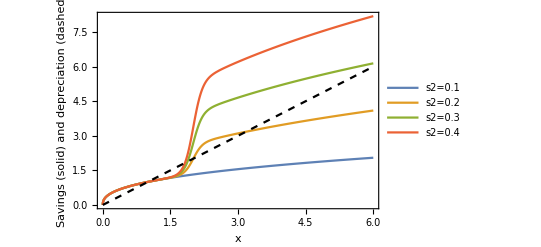

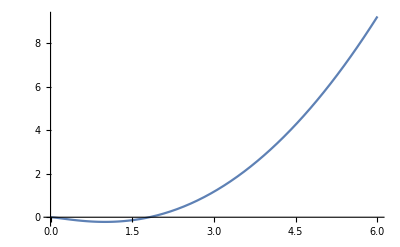
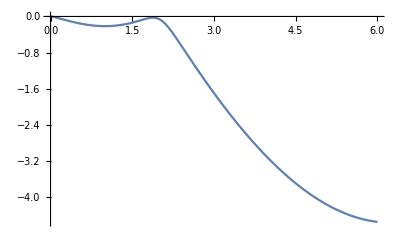
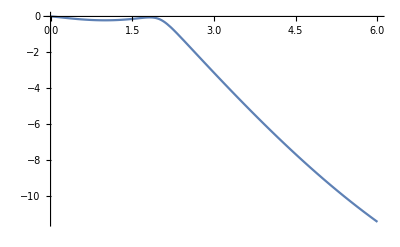
{-Graphics-,-Graphics-,-Graphics-,-Graphics-}

```mathematica
A=10;α1=0.4;s1=0.1;s3=10;d=2;δP=0.5;n=0.5;

f[x_]:=A x^α1;
s[x_]:=s1+(s2-s1)/(1+Exp[-s3 (x-d)]); 
Depreciation[x_]:=(δP+n) x
Savings[x_]:=s[x] f[x]

Valuess2={0.1,0.2,0.3,0.4};
p1=Plot[Evaluate[Table[Savings[x], {s2, Valuess2}]], {x,0,6},
Frame->True, FrameLabel->{"x", "Savings (solid) and
 depreciation (dashed)"},
LabelStyle->Medium,PlotLegends->Placed[Table[Row[{"s2=",x}],{x,Valuess2}],{Left,Top}]];
p2=Plot[Depreciation[x],{x,0,6},PlotStyle->{Black,Dashed}];
Show[{p1,p2}]

Evaluate[Table[int=NDSolveValue[{U'[x]==-(f[x]s[x] -Depreciation[x]),U[0]==0},U,{x,0,6}];
Plot[int[x],{x,0,6}],{s2, Valuess2}]]
(* int:=NDSolveValue[{U'[x]==-(Savings[x] -Depreciation[x]),U[0]==0},U,{x,0,8}]
Plot[Evaluate@Table[int[x],{s2, Valuess2}],{x,0,8},PlotRange->{-4,10}] *)
```

#### Parameter s3

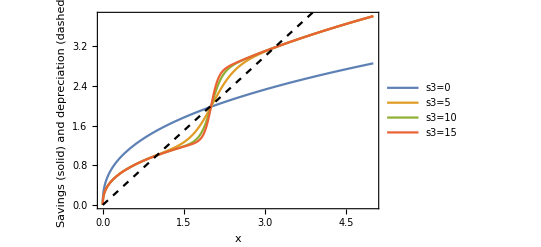

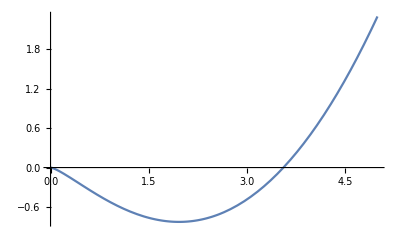
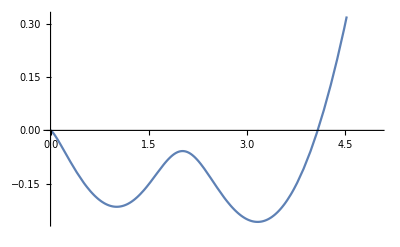
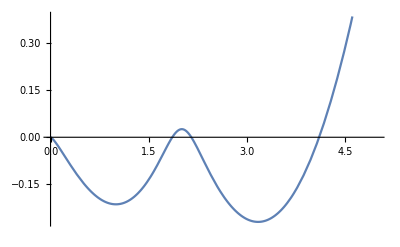
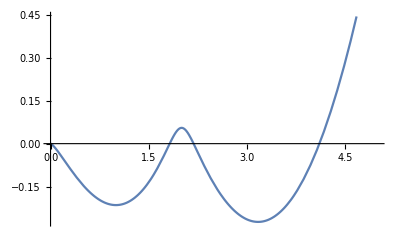

```mathematica
A=10;α1=0.4;s1=0.1;s2=0.2;d=2;δP=0.5;n=0.5;

f[x_]:=A x^α1;
s[x_]:=s1+(s2-s1)/(1+Exp[-s3 (x-d)]); 
Depreciation[x_]:=(δP+n) x
Savings[x_]:=s[x] f[x]

Valuess3={0,5, 10,15}; 
p1=Plot[Evaluate[Table[Savings[x], {s3, Valuess3}]], {x,0,5},
Frame->True, FrameLabel->{"x", "Savings (solid) and
 depreciation (dashed)"},
LabelStyle->Medium,PlotLegends->Placed[Table[Row[{"s3=",x}],{x,Valuess3}],{Right,Bottom}]];
p2=Plot[Depreciation[x],{x,0,5},PlotStyle->{Black,Dashed}];
Show[{p1,p2}]

Evaluate[Table[int=NDSolveValue[{U'[x]==-(f[x]s[x] -Depreciation[x]),U[0]==0},U,{x,0,5}];
Plot[int[x],{x,0,5}],{s3, Valuess3}]]
(* int:=NDSolveValue[{U'[x]==-(Savings[x] -Depreciation[x]),U[0]==0},U,{x,0,8}]
Plot[Evaluate@Table[int[x],{s3, Valuess3}],{x,0,8},PlotRange->{-4,10}] *)
```

#### Parameter d

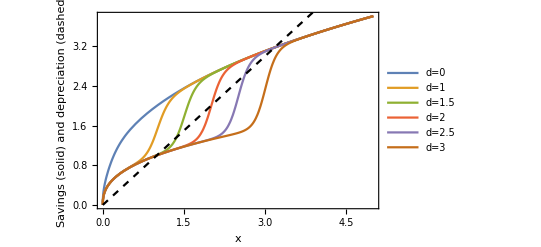

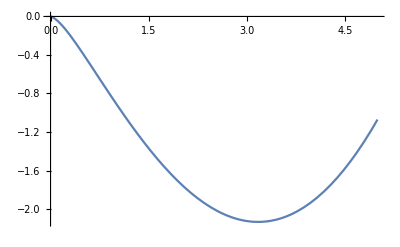
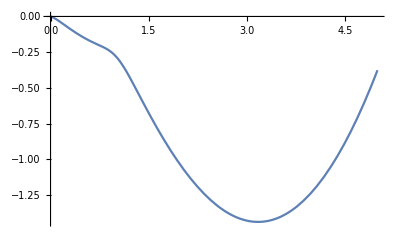
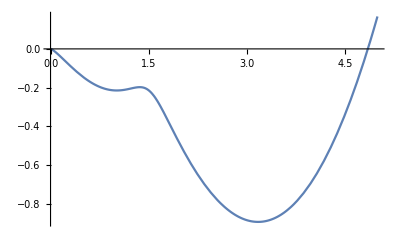
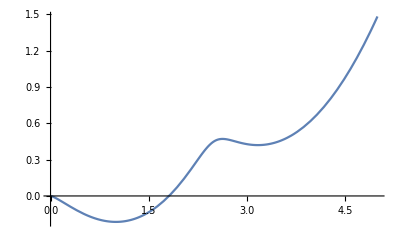
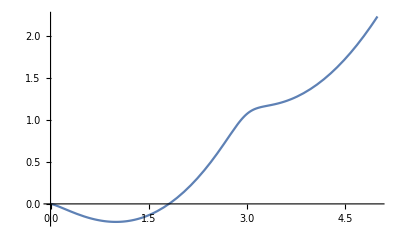
{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-}

```mathematica
A=10;α1=0.4;s1=0.1;s2=0.2;s3=10;δP=0.5;n=0.5;

f[x_]:=A x^α1;
s[x_]:=s1+(s2-s1)/(1+Exp[-s3 (x-d)]); 
Depreciation[x_]:=(δP+n) x
Savings[x_]:=s[x] f[x]

Valuesd={0,1,1.5,2,2.5,3};
p1=Plot[Evaluate[Table[Savings[x], {d, Valuesd}]], {x,0,5},
Frame->True, FrameLabel->{"x", "Savings (solid) and
 depreciation (dashed)"},
LabelStyle->Medium,PlotLegends->Placed[Table[Row[{"d=",x}],{x,Valuesd}],{Right,Bottom}]];
p2=Plot[Depreciation[x],{x,0,5},PlotStyle->{Black,Dashed}];
Show[{p1,p2}]

Evaluate[Table[int=NDSolveValue[{U'[x]==-(f[x]s[x] -Depreciation[x]),U[0]==0},U,{x,0,5}];
Plot[int[x],{x,0,5}],{d, Valuesd}]]
(* int:=NDSolveValue[{U'[x]==-(Savings[x] -Depreciation[x]),U[0]==0},U,{x,0,8}]
Plot[Evaluate@Table[int[x],{d, Valuesd}],{x,0,8},PlotRange->{-4,10}] *)
```

#### Parameter δP or n

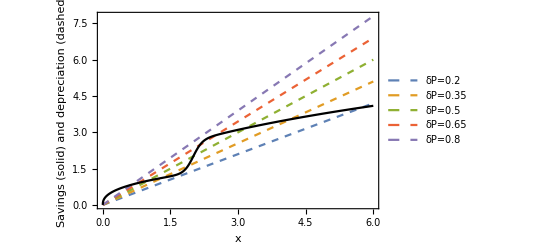

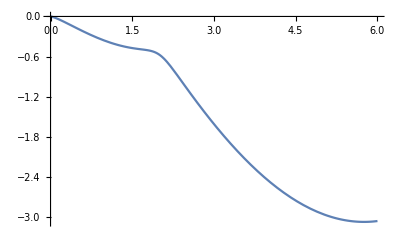
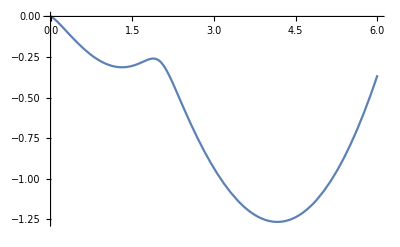
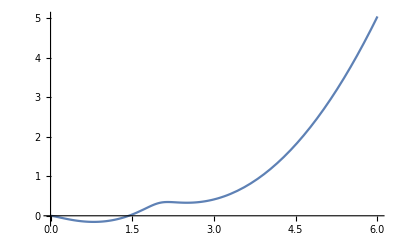
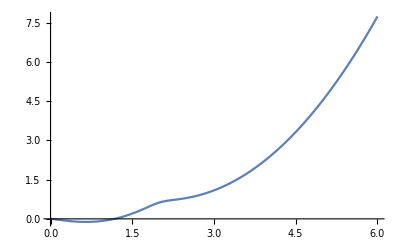
{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-}

```mathematica
A=10;α1=0.4;s1=0.1;s2=0.2;s3=10;d=2;n=0.5;

f[x_]:=A x^α1;
s[x_]:=s1+(s2-s1)/(1+Exp[-s3 (x-d)]); 
Depreciation[x_]:=(δP+n) x
Savings[x_]:=s[x] f[x]

ValuesδP={0.2,0.35,0.5,0.65,0.8};
p1=Plot[Evaluate[Table[Depreciation[x], {δP, ValuesδP}]], {x,0,6},PlotStyle->Dashed,
Frame->True, FrameLabel->{"x", "Savings (solid) and
 depreciation (dashed)"},
LabelStyle->Medium,PlotLegends->Placed[Table[Row[{"δP=",x}],{x,ValuesδP}],{Left,Top}]];
p2=Plot[Savings[x],{x,0,6},PlotStyle->Black];
Show[{p1,p2}]

Evaluate[Table[int=NDSolveValue[{U'[x]==-(f[x]s[x] -Depreciation[x]),U[0]==0},U,{x,0,6}];
Plot[int[x],{x,0,6}],{δP, ValuesδP}]]
(* int:=NDSolveValue[{U'[x]==-(Savings[x] -Depreciation[x]),U[0]==0},U,{x,0,8}]
Plot[Evaluate@Table[int[x],{δP, ValuesδP}],{x,0,8},PlotRange->{-4,10}] *)
```

## Changing s(x) / δp(x)

### Changing depreciation function δp(x)

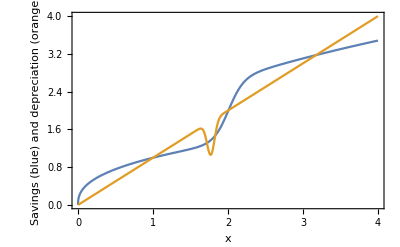

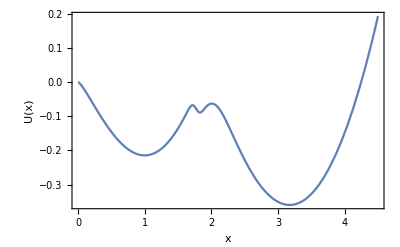

NIntegrate::nlim: y = 0.459834 x is not a valid limit of integration.

General::stop: Further output of NIntegrate::nlim will be suppressed during this calculation.

{τ→0.182516}

NIntegrate::nlim: y = 0.459834 x is not a valid limit of integration.

General::stop: Further output of NIntegrate::nlim will be suppressed during this calculation.

{τ→1.85443}

```mathematica
ClearAll[δP,f,s,Depreciation,U,int,int2,sol,τ];

A=10;α1=0.4;s1=0.1;s2=0.2;s3=10;d=2;n=0.5;
δ1=0.4;δ2=200;δ3=1.77;

f[x_]:=A x^α1;
s[x_]:=s1+(s2-s1)/(1+Exp[-s3 (x-d)]); 
(* δP[x_]:=If[x<1.8&&x>1.7,0,0.5]; *)
δP[x_]:=0.5-δ1 Exp[-δ2 (x-δ3)^2];
Depreciation[x_]:=(δP[x]+n) x;

(* min1=#&@@FindRoot[f[x]s[x]==Depreciation[x],{x,1}]
min2=#&@@FindRoot[f[x]s[x]==Depreciation[x],{x,2}]
min3=#&@@FindRoot[f[x]s[x]==Depreciation[x],{x,3}] *)

Plot[{f[x] s[x],Depreciation[x]},{x,0,4},Frame->True, FrameLabel->{"x", "Savings (blue) and
 depreciation (orange)"}]

int=NDSolveValue[{U'[x]==-(f[x]s[x] -Depreciation[x]),U[0]==0},U,{x,0,4.5}];
Plot[int[x],{x,0,4.5},Frame->True,FrameLabel->{"x","U(x)"},Axes->False]
 
L=3.17478-1.00008;
int2[x_?NumericQ]:=int[x/L];
sol=FindRoot[τ==L NIntegrate[Exp[-int2[x]] NIntegrate[Exp[int[y]],{y,x/L,1}],{x,1.00008,3.17478}] ,{τ,1}]
sol=FindRoot[τ==L NIntegrate[Exp[-int2[x]] NIntegrate[Exp[int[y]],{y,x/L,1}],{x,0,3}] ,{τ,1}]
```

### Changing savings rate s(x)

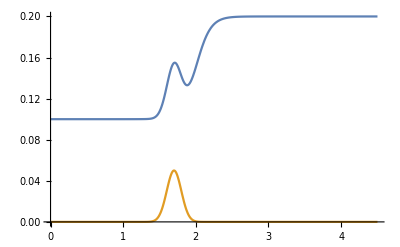

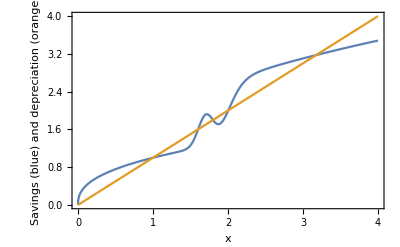

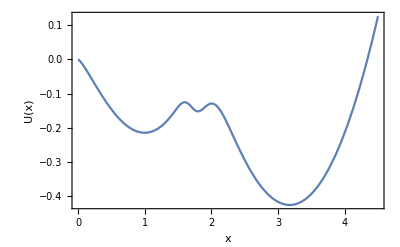

NIntegrate::nlim: y = 0.459834 x is not a valid limit of integration.

General::stop: Further output of NIntegrate::nlim will be suppressed during this calculation.

{τ→0.182445}

```mathematica
ClearAll[f,s,Depreciation,U,int,int2,sol,τ];

A=10;α1=0.4;s1=0.1;s2=0.2;s3=10;s4=0.05;s5=50;d1=2;d2=1.7;δP=0.5;n=0.5;

f[x_]:=A x^α1;
s[x_]:=s1+(s2-s1)/(1+Exp[-s3 (x-d1)])+s4 Exp[-s5 (x-d2)^2]; 
Depreciation[x_]:=(δP+n) x

(* min1=#&@@FindRoot[f[x]s[x]==Depreciation[x],{x,1}]
min2=#&@@FindRoot[f[x]s[x]==Depreciation[x],{x,2}]
min3=#&@@FindRoot[f[x]s[x]==Depreciation[x],{x,3}] *)

Plot[{s[x],s4 Exp[-s5 (x-d2)^2]},{x,0,4.5}]

Plot[{f[x] s[x],Depreciation[x]},{x,0,4},Frame->True, FrameLabel->{"x", "Savings (blue) and
 depreciation (orange)"}]

int=NDSolveValue[{U'[x]==-(f[x]s[x] -Depreciation[x]),U[0]==0},U,{x,0,4.5}];
Plot[int[x],{x,0,4.5},Frame->True,FrameLabel->{"x","U(x)"},Axes->False]

int2[x_?NumericQ]:=int[x/L];
sol=FindRoot[τ==L NIntegrate[Exp[-int2[x]] NIntegrate[Exp[int[y]],{y,x/L,1}],{x,1.00008,3.17478}] ,{τ,1}]
```

#### Calculating MFPTs for some random plots

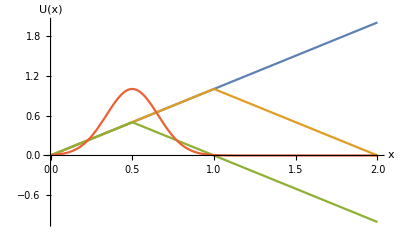

Power::infy: Infinite expression 1/0. encountered.

NIntegrate::nlim: y = 10. x is not a valid limit of integration.

General::stop: Further output of NIntegrate::nlim will be suppressed during this calculation.

Power::infy: Infinite expression 1/0. encountered.

General::stop: Further output of Power::infy will be suppressed during this calculation.

Infinity::indet: Indeterminate expression 0. ComplexInfinity encountered.

General::stop: Further output of Infinity::indet will be suppressed during this calculation.

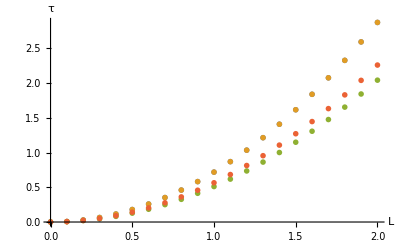

```mathematica
ClearAll[U,U2,τ,L];

Ulin[x_]:=x;
U2lin[x_?NumericQ]:=Ulin[x/L]

Utria[x_]:=If[x<1,x,2-x];
U2tria[x_?NumericQ]:=Utria[x/L];

UtriaS[x_]:=If[x<0.5,x,1-x];
U2triaS[x_?NumericQ]:=UtriaS[x/L];

Uexp[x_]:=Exp[-20 (x-0.5)^2];
U2exp[x_?NumericQ]:=Uexp[x/L]

Plot[{Ulin[x],Utria[x],UtriaS[x],Uexp[x]},{x,0,2},AxesLabel->{"x","U(x)"}]
ListPlot[{Transpose[{Range[0,2,0.1],Table[sol=FindRoot[τ==L NIntegrate[Exp[-U2lin[x]] NIntegrate[Exp[Ulin[y]],{y,x/L,1}],{x,0,L}] ,{τ,1}];
τ=τ/.sol,{L,0,2,0.1}]}],Transpose[{Range[0,2,0.1],Table[sol=FindRoot[τ==L NIntegrate[Exp[-U2tria[x]] NIntegrate[Exp[Utria[y]],{y,x/L,1}],{x,0,L}] ,{τ,1}];
τ=τ/.sol,{L,0,2,0.1}]}],Transpose[{Range[0,2,0.1],Table[sol=FindRoot[τ==L NIntegrate[Exp[-U2triaS[x]] NIntegrate[Exp[UtriaS[y]],{y,x/L,1}],{x,0,L}] ,{τ,1}];
τ=τ/.sol,{L,0,2,0.1}]}],
Transpose[{Range[0,2,0.1],Table[sol=FindRoot[τ==L NIntegrate[Exp[-U2exp[x]] NIntegrate[Exp[Uexp[y]],{y,x/L,1}],{x,0,L}] ,{τ,1}];
τ=τ/.sol,{L,0,2,0.1}]}]},PlotMarkers->"OpenMarkers",AxesLabel->{"L","τ"},Ticks->Table[L,{L,0,2,0.1}]]

(* doesn't make sense *)
```